Universidad de Jaén. EPS Jaén.
Departamento de Matemáticas. Grado en Ingeniería Informática
Análisis y Métodos Numéricos.

## Problemas. Tema 4. Funciones reales

## 1.- Dada la función f(x) = (x^3 - 2 x + 4)/(x^2 - 4), determinar ( a ) Los puntos de discontinuidad y su clasificación ( b ) Asíntotas verticales , horizontales y oblícuas

Solución: 
Apartado a)
Como se trata de una función racional, función cociente de polinomios, sabemos que la función es continua en todo su dominio, es decir, todo R menos los puntos que anulan el denominador. En este caso, x^2 - 4=0⟺x^2 = 4⟺x=±2
La función es continua en ∀x∈ℝ-{-2,2} en los puntos x=-2 y x=2, la función no esta definida por lo que se trata de una discontinuidad evitable.

Apartado b)
■ Asíntotas verticales
	Los candidatos a asíntota vertical son los puntos que no son del dominio, es decir, las posibles asíntotas se encuentran en x=-2 y x=2. Para ello estudiemos su límite
	Lim_(x->-2)(x^3 - 2 x + 4)/(x^2 - 4)=[0/0]=Lim_(x->-2)((x+2)(x^2-2x+2))/((x-2)(x+2))=Lim_(x->-2)(x^2-2x+2)/(x-2)=-5/2 x=-2 no es una asíntota vertical
	Lim_(x->-2)(x^3 - 2 x + 4)/(x^2 - 4)=Lim_(x->2)((x+2)(x^2-2x+2))/((x-2)(x+2))=Lim_(x->2)(x^2-2x+2)/(x-2) Debemos estudiar los límites laterales
		Lim_(x->2^-)(x^2-2x+2)/(x-2)=-∞
		Lim_(x->2^+)(x^2-2x+2)/(x-2)=+∞
	La función tiene una asintota vertical en x=2
	
■ Asíntotas horizontales
	Diremos que la función f(x) tiene asíntota horizontal si la función tiende a un número cuando nos alejamos a ±∞
	Lim_(x->∞)(x^3 - 2 x + 4)/(x^2 - 4)=Lim_(x->∞)x^3/x^2=Lim_(x->∞)x=∞
	Lim_(x->-∞)(x^3 - 2 x + 4)/(x^2 - 4)=Lim_(x->-∞)x^3/x^2=Lim_(x->-∞)x=-∞
	La función no tiene asintota horizontal

■ Asíntotas oblicuas
	Diremos que la función f(x) tiene una asíntota oblicua de la forma y=mx+n con m=Lim_(x->∞)(f(x))/x y n=Lim_(x->∞)f(x)-mx
	m=Lim_(x->∞)(f(x))/x=Lim_(x->∞)((x^3 - 2 x + 4)/(x^2 - 4))/x=Lim_(x->∞)(x^3 - 2 x + 4)/(x^3 - 4x)=Lim_(x->-∞)x^3/x^3=Lim_(x->-∞)1=1
	n=Lim_(x->∞)f(x)-mx=Lim_(x->∞)(x^3 - 2 x + 4)/(x^2 - 4)-x=Lim_(x->∞)(x^3 - 2 x + 4)/(x^2 - 4)-(x^3 - 4x)/(x^2 - 4)0=Lim_(x->∞)(2 x + 4)/(x^2 - 4)=Lim_(x->∞)(2 x)/x^2=Lim_(x->∞)2/x=0
	Por tanto, la función tiene una asíntota oblicua en y=x
	
	Pintemos la gráfica con Mathematica:

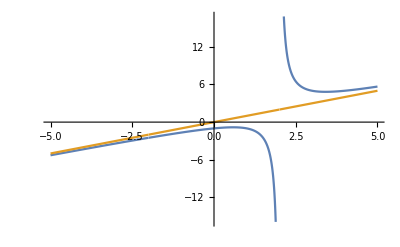

```mathematica
Plot[{(x^3-2x+4)/(x^2-4),x},{x,-5,5}]
```

Con el Mathematica:

```mathematica
Factor[x^3-2x+4]
```

(2+x) (2-2 x+x^2)

```mathematica
f[x_]:=(x^3-2x+4)/(x^2-4)
```

Asintota vertical

```mathematica
Limit[f[x],x->-2]
```

-5/2

```mathematica
Limit[f[x],x->2]
```

Indeterminate

Asintota horizontal

```mathematica
Limit[f[x],x->Infinity]
```

∞

```mathematica
Limit[f[x],x->-Infinity]
```

-∞

Asintota oblicua

```mathematica
Limit[f[x]/x,x->Infinity]
```

1

```mathematica
Limit[f[x]-x,x->Infinity]
```

0

## 2.- Estudia el signo de la función f(x) = (x^2 - 4)/x

Solución:
El procedimiento para estudiar los signos de una función es:
	1) Estudiar el dominio de la función.
	2) Estudiar dónde la función es continua.
	3) Estudiar dónde se anula la función.
	4) Formamos los intervalos de signos.


1)  Estudiamos el dominio de la función. 
Como se trata de una función racional definida como el cociente de dos polinomios, sabemos que el dominio es todo R menos los puntos que anulan el denominador, es decir, donde x=0. Por tanto, el domino es ℝ - { 0}.

2) Estudiemos la continuidad. 
La función es continua en todo el dominio, por ser el cociente de polinomios, que son funciones continuas. 
Por tanto, la función es continua en ℝ - {0}.

3) Estudiemos cuándo se anula la función. Como es un cociente, estudiamos cuándo se anula el numerador. 
	x^2- 4=0 ⟹ x^2= 4 ⟹ x=2 ó x=-2. La función se anula en {-2, 2}.

4) Formamos los intervalos de signos.
Ahora consideramos toda la recta real y marcamos el dominio, las discontinuidades y los ceros de la función. Dividimos así ela recta R en cuatro intervalos: (-∞, -2), (-2,0), (0,2), (2, ∞). Sabemos que en cada uno de estos intervalos la función tiene un solo signo, es decir, la función no cambia de signo en el intervalo. Basta ahora evaluar la función en un punto de cada uno de ellos.
	Intervalo (-∞, -2)⟹f(-10)=((-10)^2 - 4)/-10<0
	Intervalo (-2,0)⟹f(-1)=((-1)^2 - 4)/-1>0
	Intervalo (0,2)⟹f(1)=(1^2 - 4)/1<0
	Intervalo (2,∞)⟹ f(10)=(10^2 - 4)/10>0
Por tanto, f es positiva en  (-2,0)∪(2,∞) y es negativa en (-∞,-2)∪(-2,0). Se anula en los puntos -2 y 2.

Con Mathematica podemos pintar la gráfica y ver la situación

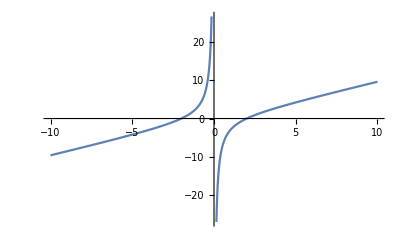

```mathematica
Plot[(x^2-4)/x,{x,-10,10}]
```

## 3.- Encontrar una función continua y periódica que aproxime la diferencia de la marea a lo largo del día. Sabiendo que la marea alta ha llegado a 8m y la baja se quedó en 2m,que tiene un período de 12 y que el menor estado de la marea se alcance en (1+π)/2.

Solución: 
Buscamos una función de la forma f(x)=Acos(Bx+C)+D, donde
	◼ A es la Amplitud. Indica la máxima oscilación posible con respecto al valor medio, es decir, es el punto medio entre el máximo y el mínimo
	◼  B es la cantidad de ciclos, esto es, el número de veces que se repite la gráfica 2πrad
	◼  C indica la traslación en el eje de abscisas
	◼  D es el valor medio en torno al cual oscila la función
	◼  T es el Periodo, la medida del ángulo en el cual se completa un ciclo, esto es T=(2π)/(|B|)

Sabiendo esto, los datos que nos dan son:
	● Máx: 8
	● Min: 2
	● T=12
	● f((1+π)/2)=2

D=(8+2)/2=5
Como la función tiene un máximo de 8: A*Cos(1)+5=8⟹A+5=8⟹A=3
Como la función tiene un mínimo de 2: A*Cos(-1)+5=2⟹-A+5=2⟹A=3
T=12⟹(2π)/(|B|)=12⟹B=±π/6
Hasta aquí, se tiene que 
	▫Si B=π/6 ⟹f(x)=2Cos(π/6 x+C)+5, imponemos que pase por el punto f((1+π)/2)=2. Esto es, f((1+π)/2)=2⟹3Cos(π/6*(1+π)/2+C)+5=2⟹Cos((π(1+π))/12+C)=-1⟹(π(1+π))/12+C=π⟹C=-(1+π)/12
	La función pedida es f(x)=3Cos(π/6 x-(1+π)/12)+5
	▫Si B=π/6 ⟹f(x)=2Cos(-π/6x+C)+5, imponemos que pase por el punto f((1+π)/2)=2. Esto es, f((1+π)/2)=2⟹3Cos(-π/6*(1+π)/2+C)+5=2⟹Cos((-π(1+π))/12+C)=-1⟹-(π(1+π))/12+C=π⟹C=(1+π)/12
	La función pedida es f(x)=3Cos((1+π)/12-π/6 x)+5
	
Pintemos con Mathematica la gráfica

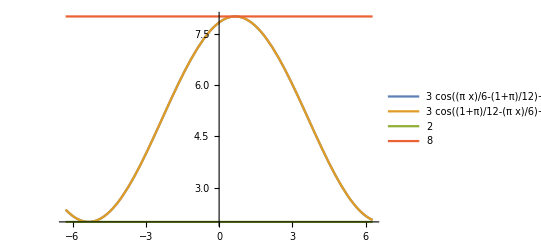

```mathematica
grafica=Plot[{3*Cos[Pi*x/6-(1+Pi)/12]+5,3*Cos[(1+Pi)/12-Pi*x/6]+5,2,8},{x,-2Pi,2Pi}, PlotLegends->"Expressions"]
```

## 4.- Tiene la ecuación x^3+x=1 una raíz en el intervalo [0,1]

Solución :
Consideramos la función f(x)=x^3+x-1, una función continua en todo R por ser un polinomio, es especial continua en el intervalo [0,1]. además, tenemos que 
	f(0)=-1<0
	f(1)=1+1-1=1>0
es decir, la función cambia de signo en el intervalo [0,1] entonces el Teorema de Bolzano nos asegura que la función f(x) tiene, al menos, una raíz en el intervalo [0,1].

Podemos pintar la situación usando Mathematica

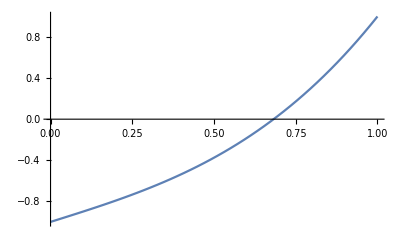

```mathematica
Plot[x^3+x-1,{x,0,1}]
```

## 5.- (Junio 2021) Calcular el dominio de la función log(√(x+1))

(log, Log o Ln siempre se refiere al logaritmo neperiano o natural. Si en alguna ocasión hiciese falta referirse al logaritmo decimal, en base 2, u otra, se especificará.)

Solución: 
El logaritmo se puede calcular de números mayores estrictamente que cero. La raíz cuadrada de un número es estrictamente mayor que cero si el número al que se calcula es mayor estrictamente que cero. Como la cantidad a la que hay que calcular la raíz cuadrada es x+1, concluimos que es necesario que x+1 >0. Es decir, x>-1.

El dominio de la función sería (-1,∞).
Si x∈(-1,∞), x+1 ∈(0,∞) y √(x+1) >0 y el logaritmo se puede calcular. 

De otra forma:
La primera operación es x+1, que puede realizarse para cualquier valor de x. Dom (x+1) = ℝ.
A continuación hay que realizar la raíz cuadrada. Para ello, se necesita que x+1 ≥0. Así,  Dom (√(x+1)) = [-1,∞).
Finalmente, la última operación es el logaritmo. Para calcular el logaritmo es necesario que la cantidad sea mayor estricta que cero. √(x+1) > 0 si (x+1) > 0, es decir x>-1.  

Por tanto, Dom (log( √(x+1) )) = (-1, ∞).

Con el Mathematica:

```mathematica
f[x_]:=Log[Sqrt[(x+1)]]
```

```mathematica
FunctionDomain[f[x],x]
```

x>-1

## 6.- Calcula el dominio de definición de la función f(x)=√((x + 1)/(e^x - 1))

Solución: 
La  función f(x) es una función radical de exponente par (raíz cuadrada), estas funciones están definidas cuando el radicando pertenece a los reales positivos incluido el cero, esto es, (x + 1)/(e^x - 1)∈ℝ_0^+, es decir, cuando
(x + 1)/(e^x - 1)⩾0. Esto se cumple en dos ocasiones:
	1) Si x + 1⩾0 y e^x - 1>0
	2) Si x + 1⩽0 y e^x - 1<0
	
Estudiemos cada una de ellas
	1) Si x + 1⩾0 y e^x - 1>0
	x + 1⩾0⟺x⩾-1⟺x∈[-1,∞)
e^x - 1>0⟺e^x>1⟺x>Ln(1)=0⟺x∈(0,∞)}⟹x∈(0,∞)
	
	2) Si x + 1⩽0 y e^x - 1<0
	x + 1⩽0⟺x⩽-1⟺x∈(-∞,-1]
e^x - 1<0⟺e^x<1⟺x<Ln(1)=0⟺x∈(-∞,0)}⟹x∈(-∞,-1]

Así, el dominio de definición de la función es Dom(f(x))=(-∞,-1]∪(0,∞)

Con el Mathematica:

```mathematica
f[x_]:=Sqrt[(x+1)/(Exp[x]-1)]
```

```mathematica
FunctionDomain[f[x],x]
```

x≤-1||x>0

## 7.- Dar la expresión de una función periódica y continua expresada en términos del cos(x) que pasa por el punto (1,-1), tiene un periodo de 2π, valor mínimo -5 y máximo de -1. (Con Mathematica) Realizar la representación gráfica de dicha función en el intervalo [-2π, 2π].

Solución: 
Buscamos una función de la forma f(x)=Acos(Bx+C)+D, donde
	◼ A es la Amplitud. Indica la máxima oscilación posible con respecto al valor medio, es decir, es el punto medio entre el máximo y el mínimo
	◼  B es la cantidad de ciclos, esto es, el número de veces que se repite la gráfica 2πrad
	◼  C indica la traslación en el eje de abscisas
	◼  D es el valor medio en torno al cual oscila la función
	◼  T es el Periodo, la medida del ángulo en el cual se completa un ciclo, esto es T=(2π)/(|B|)

Sabiendo esto, los datos que nos dan son:
	● f(1)=-1
	● T=2π
	● Máx: -1
	● Min: -5

T=2π⟹(2π)/(|B|)=2π⟹B=±1
D=(-1-5)/2=-3
Como la función tiene un máximo de -1: A*Cos(1)-3=-1⟹A-3=-1⟹A=2
Como la función tiene un mínimo de -5: A*Cos(-1)-3=-5⟹-A-3=-5⟹A=2
Hasta aquí, se tiene que 
	▫Si B=1 ⟹f(x)=2Cos(x+C)-3, imponemos que pase por el punto (1,-1). Esto es, f(1)=-1⟹2Cos(1+C)-3=-1⟹Cos(1+C)=1⟹1+C=0⟹C=-1
	La función pedida es f(x)=2Cos(x-1)-3
	▫Si B=-1 ⟹f(x)=2Cos(C-x)-3, imponemos que pase por el punto (1,-1). Esto es, f(1)=-1⟹2Cos(C-1)-3=-1⟹Cos(C-1)=1⟹C-1=0⟹C=1
	La función pedida es f(x)=2Cos(1-x)-3
	
Pintemos con Mathematica la gráfica

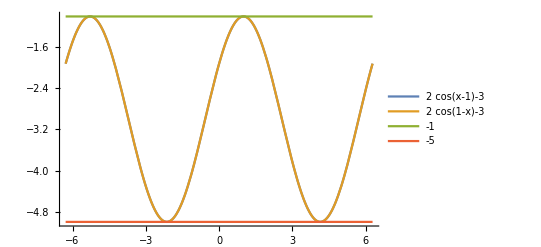

```mathematica
grafica=Plot[{2*Cos[x-1]-3,2*Cos[1-x]-3,-1,-5},{x,-2Pi,2Pi}, PlotLegends->"Expressions"]
```

## 8.- (Julio 2023) Para resolver la ecuación x^3+x=1 consideramos la función f(x)= x^3+x-1. A continuación, evaluamos f(x) en algunos puntos en x=0, en x=1. Estudiar si podemos usar el método de Bisección y aplicarlo tres veces.

Solución: 
La función f(x) = x^3+x-1 es polinómica. Por tanto, f es continua y derivable cuantas veces queramos en toda la recta real.
Evaluamos f en 0 y 1: f(0)=-1, f(1)=1. Como la función es continua en [0,1] y hay cambio de signo de la función en los extremos, podemos asegurar que la función se anula en algún punto del interior y podemos aproximarlo por el método de bisección.

Comenzamos por el intervalo [0,1]. 
f(0)<0, f(1)>0. El punto medio es (0+1)/2=1/2. f(1/2) = (1/2)^3+(1/2)-1= 1/8 + 1/2 - 1 < 0. Hay cambio de signo en el intervalo [1/2,1]
f(1/2)<0, f(1)>0. El punto medio es (1/2 + 1)/2=3/4. f(3/4) = (3/4)^3+(3/4)-1 = 27/64 + 3/4 - 1 = 27/64 + 48/64 - 64/64 = 11/64 > 0. Hay cambio de signo en el intervalo [1/2, 3/4].
f(1/2)<0, f(3/4)>0. El punto medio es (1/2 + 3/4) / 2 = 5/8. f(5/8) = (5/8)^3+(5/8)-1= 125/512 + 5/8 - 1 = 125/512 + 320/512 - 512/512 = (445-512)/512< 0. Hay cambio de signo en el intervalo [5/8,3/4].